```mathematica
Needs["Constants`"]
Needs["Utilities`"]
Needs["EnergyLoss`"]
```

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23}

#### Load params

```mathematica
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
```

#### tests

```mathematica
"qF"/.SiO2Totalparams
"qF"/.MgOTotalparams
```

{2.2927×10^10,3.90562×10^10}

{1.64516×10^10,2.19692×10^10,2.34828×10^10,3.63218×10^10}

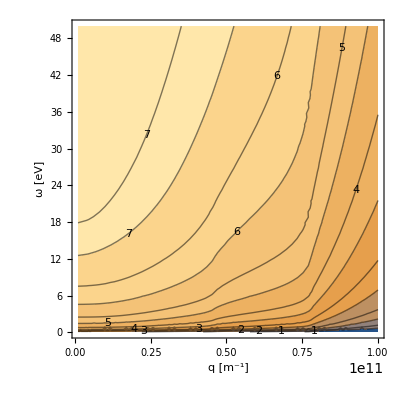

```mathematica
ContourTotalParamsωq[SiO2Totalparams,"SiO2"]
```

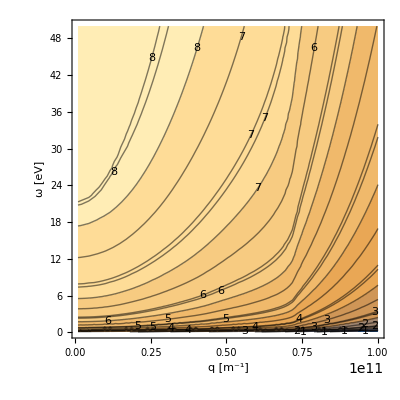

```mathematica
ContourTotalParamsωq[MgOTotalparams,"MgO"]
```

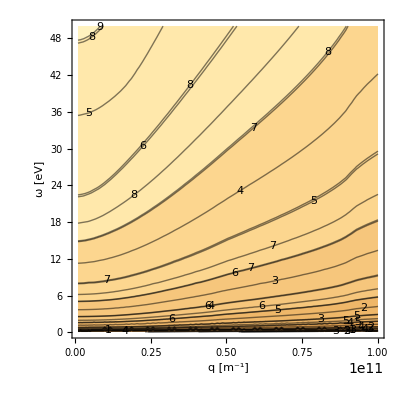

```mathematica
ContourTotalParamsωq[FeTotalparams,"Fe"]
```

```mathematica
testcutoff[ω_,l_]:=If[l<0,HeavisideTheta["ωBG"-ω],1]
```

```mathematica
testcutoff[ω,-1]
```

HeavisideTheta[ωBG-ω]

```mathematica
BandGapTruncation[u z 2 "qF" "vF",-1]/.SiO2Totalparams
```

{HeavisideTheta[ωBG-1.21748×10^17 u z],HeavisideTheta[ωBG-3.533×10^17 u z]}

```mathematica
EnergyLossMSIFitEnhanced[5 10^5 ("JpereV")/("c")^2/.SIConstRepl,10^-3 "c" /.SIConstRepl,Join[SiO2Totalparams[[1]],{"ωBG"->(7.7 "JpereV")/("ℏ")/.SIConstRepl}],-1]
```

For mχ = 8.9×10^-31 , vχ = 300000
L:	0.0449786 
Prefactor:	8.35673×10^13
dEdr:	3.75874×10^12

<|mχ→8.9×10^-31,vχ→300000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωBG→1.16923×10^16},L→0.0449786,Prefactor→8.35673×10^13,dEdr→3.75874×10^12|>

```mathematica
EnergyLossMSIFitEnhanced[5 10^5 ("JpereV")/("c")^2/.SIConstRepl,10^-3 "c" /.SIConstRepl,Join[SiO2Totalparams[[1]],{"ωBG"->(7.7 "JpereV")/("ℏ")/.SIConstRepl}],1]
```

For mχ = 8.9×10^-31 , vχ = 300000
L:	0.0449786 
Prefactor:	8.35673×10^13
dEdr:	3.75874×10^12

<|mχ→8.9×10^-31,vχ→300000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωBG→1.16923×10^16},L→0.0449786,Prefactor→8.35673×10^13,dEdr→3.75874×10^12|>

```mathematica
1/(2 ("ℏ"/.SIConstRepl))(5 10^5 ("JpereV")/("c")^2/.SIConstRepl)(10^-3 "c" /.SIConstRepl)^2
(7.7 "JpereV")/("ℏ")/.SIConstRepl
```

3.79621×10^14

1.16923×10^16

```mathematica
EnergyLossMSIFitEnhanced[5 10^12 ("JpereV")/("c")^2/.SIConstRepl,10^-2 "c" /.SIConstRepl,Join[SiO2Totalparams[[1]],{"ωBG"->(7.7 "JpereV")/("ℏ")/.SIConstRepl}],-1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0847641}. NIntegrate obtained 0.0498877 and 2.76396×10^-7 for the integral and error estimates.

For mχ = 8.9×10^-24 , vχ = 3000000
L:	0.0498877 
Prefactor:	8.35673×10^11
dEdr:	4.16898×10^10

<|mχ→8.9×10^-24,vχ→3000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωBG→1.16923×10^16},L→0.0498877,Prefactor→8.35673×10^11,dEdr→4.16898×10^10|>

```mathematica
EnergyLossMSIFitEnhanced[5 10^12 ("JpereV")/("c")^2/.SIConstRepl,10^-2 "c" /.SIConstRepl,Join[SiO2Totalparams[[1]],{"ωBG"->(7.7 "JpereV")/("ℏ")/.SIConstRepl}],1]
```

For mχ = 8.9×10^-24 , vχ = 3000000
L:	0.145776 
Prefactor:	8.35673×10^11
dEdr:	1.21821×10^11

<|mχ→8.9×10^-24,vχ→3000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωBG→1.16923×10^16},L→0.145776,Prefactor→8.35673×10^11,dEdr→1.21821×10^11|>

```mathematica
1/(2 ("ℏ"/.SIConstRepl))(5 10^9 ("JpereV")/("c")^2/.SIConstRepl)(10^-3 "c" /.SIConstRepl)^2
(7.7 "JpereV")/("ℏ")/.SIConstRepl
```

3.79621×10^18

1.16923×10^16

```mathematica
EnergyLossMSIFitEnhanced[5 10^12 ("JpereV")/("c")^2/.SIConstRepl,10^-2 "c" /.SIConstRepl,Join[SiO2Totalparams[[1]],{"ωBG"->(7.7 "JpereV")/("ℏ")/.SIConstRepl}],0]
```

For mχ = 8.9×10^-24 , vχ = 3000000
L:	0.133197 
Prefactor:	1.04228×10^10
dEdr:	1.38829×10^9

<|mχ→8.9×10^-24,vχ→3000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωBG→1.16923×10^16},L→0.133197,Prefactor→1.04228×10^10,dEdr→1.38829×10^9|>

## Pre ω fix

### Compute contribution from below the band gap

#### Run SiO2

```mathematica
SiO2TotalparamsBG=Table[Join[SiO2Totalparams[[i]],{"ωBG"->(8.96 "JpereV")/("ℏ")/.SIConstRepl}],{i,Length[SiO2Totalparams]}];
```

```mathematica
SiO2BGeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,SiO2TotalparamsBG,True,"SiO2BGeDictSI",-1]
```

1 of 32

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000175393 
Prefactor:	2.08918×10^15
dEdr:	3.66428×10^11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.00006384 and 2.53169×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.00006384 
Prefactor:	2.77438×10^15
dEdr:	1.77116×10^11

dEdr total: 5.43545×10^11

2 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.001771 and 0.0000717928 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.001771 
Prefactor:	2.08918×10^13
dEdr:	3.69994×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000631085 and 0.0000248038 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000631085 
Prefactor:	2.77438×10^13
dEdr:	1.75087×10^10

dEdr total: 5.45081×10^10

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0172835 
Prefactor:	2.08918×10^11
dEdr:	3.61084×10^9

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.00660997 
Prefactor:	2.77438×10^11
dEdr:	1.83385×10^9

dEdr total: 5.44469×10^9

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.147065 
Prefactor:	2.08918×10^9
dEdr:	3.07246×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.0603712 
Prefactor:	2.77438×10^9
dEdr:	1.67493×10^8

dEdr total: 4.74739×10^8

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000797277 
Prefactor:	2.08918×10^15
dEdr:	1.66566×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000305998 
Prefactor:	2.77438×10^15
dEdr:	8.48955×10^11

dEdr total: 2.51461×10^12

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00796714 
Prefactor:	2.08918×10^13
dEdr:	1.66448×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00305899 
Prefactor:	2.77438×10^13
dEdr:	8.4868×10^10

dEdr total: 2.51316×10^11

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0763335 
Prefactor:	2.08918×10^11
dEdr:	1.59474×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0297804 
Prefactor:	2.77438×10^11
dEdr:	8.2622×10^9

dEdr total: 2.42096×10^10

8 of 32

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.336249 
Prefactor:	2.08918×10^9
dEdr:	7.02486×10^8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.160224 
Prefactor:	2.77438×10^9
dEdr:	4.44521×10^8

dEdr total: 1.14701×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000992502 
Prefactor:	2.08918×10^15
dEdr:	2.07352×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000394726 
Prefactor:	2.77438×10^15
dEdr:	1.09512×10^12

dEdr total: 3.16864×10^12

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0107805 
Prefactor:	2.08918×10^13
dEdr:	2.25224×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00406926 
Prefactor:	2.77438×10^13
dEdr:	1.12897×10^11

dEdr total: 3.3812×10^11

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.222922 
Prefactor:	2.08918×10^11
dEdr:	4.65726×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0876765 
Prefactor:	2.77438×10^11
dEdr:	2.43248×10^10

dEdr total: 7.08973×10^10

12 of 32

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.54487 
Prefactor:	2.08918×10^9
dEdr:	1.13833×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.281333 
Prefactor:	2.77438×10^9
dEdr:	7.80524×10^8

dEdr total: 1.91886×10^9

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.97971×10^-6 
Prefactor:	2.08918×10^15
dEdr:	6.22515×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.07087×10^-6 
Prefactor:	2.77438×10^15
dEdr:	2.97099×10^9

dEdr total: 9.19613×10^9

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00100446 
Prefactor:	2.08918×10^13
dEdr:	2.09851×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000149851 
Prefactor:	2.77438×10^13
dEdr:	4.15744×10^9

dEdr total: 2.51425×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.164744 
Prefactor:	2.08918×10^11
dEdr:	3.44181×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.0511229 
Prefactor:	2.77438×10^11
dEdr:	1.41834×10^10

dEdr total: 4.86015×10^10

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.49195 
Prefactor:	2.08918×10^9
dEdr:	1.02777×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.250223 
Prefactor:	2.77438×10^9
dEdr:	6.94213×10^8

dEdr total: 1.72199×10^9

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.27123×10^-6 
Prefactor:	2.08918×10^15
dEdr:	2.65582×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	2.16379×10^-7 
Prefactor:	2.77438×10^15
dEdr:	6.00318×10^8

dEdr total: 3.25614×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000921475 
Prefactor:	2.08918×10^13
dEdr:	1.92513×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000118986 
Prefactor:	2.77438×10^13
dEdr:	3.30113×10^9

dEdr total: 2.25524×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.16258 
Prefactor:	2.08918×10^11
dEdr:	3.3966×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.0497883 
Prefactor:	2.77438×10^11
dEdr:	1.38131×10^10

dEdr total: 4.77791×10^10

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.490025 
Prefactor:	2.08918×10^9
dEdr:	1.02375×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.249109 
Prefactor:	2.77438×10^9
dEdr:	6.91123×10^8

dEdr total: 1.71488×10^9

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.32068×10^-6 
Prefactor:	2.08918×10^15
dEdr:	2.75914×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.2805×10^-7 
Prefactor:	2.77438×10^15
dEdr:	6.32697×10^8

dEdr total: 3.39184×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000917566 
Prefactor:	2.08918×10^13
dEdr:	1.91696×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000117619 
Prefactor:	2.77438×10^13
dEdr:	3.26319×10^9

dEdr total: 2.24328×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.162468 
Prefactor:	2.08918×10^11
dEdr:	3.39425×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.0497201 
Prefactor:	2.77438×10^11
dEdr:	1.37942×10^10

dEdr total: 4.77368×10^10

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.489926 
Prefactor:	2.08918×10^9
dEdr:	1.02354×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.249053 
Prefactor:	2.77438×10^9
dEdr:	6.90966×10^8

dEdr total: 1.71451×10^9

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.32366×10^-6 
Prefactor:	2.08918×10^15
dEdr:	2.76536×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.28835×10^-7 
Prefactor:	2.77438×10^15
dEdr:	6.34875×10^8

dEdr total: 3.40024×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000917371 
Prefactor:	2.08918×10^13
dEdr:	1.91656×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000117553 
Prefactor:	2.77438×10^13
dEdr:	3.26137×10^9

dEdr total: 2.24269×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.162464 
Prefactor:	2.08918×10^11
dEdr:	3.39417×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.0497166 
Prefactor:	2.77438×10^11
dEdr:	1.37933×10^10

dEdr total: 4.77349×10^10

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.489921 
Prefactor:	2.08918×10^9
dEdr:	1.02353×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.24905 
Prefactor:	2.77438×10^9
dEdr:	6.90958×10^8

dEdr total: 1.71449×10^9

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.32381×10^-6 
Prefactor:	2.08918×10^15
dEdr:	2.76569×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.28876×10^-7 
Prefactor:	2.77438×10^15
dEdr:	6.34989×10^8

dEdr total: 3.40068×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000917355 
Prefactor:	2.08918×10^13
dEdr:	1.91652×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00011755 
Prefactor:	2.77438×10^13
dEdr:	3.26128×10^9

dEdr total: 2.24265×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.162464 
Prefactor:	2.08918×10^11
dEdr:	3.39416×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.0497164 
Prefactor:	2.77438×10^11
dEdr:	1.37932×10^10

dEdr total: 4.77348×10^10

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.489921 
Prefactor:	2.08918×10^9
dEdr:	1.02353×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.249049 
Prefactor:	2.77438×10^9
dEdr:	6.90957×10^8

dEdr total: 1.71449×10^9

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{5.43545×10^11,5.45081×10^10,5.44469×10^9,4.74739×10^8},{2.51461×10^12,2.51316×10^11,2.42096×10^10,1.14701×10^9},{3.16864×10^12,3.3812×10^11,7.08973×10^10,1.91886×10^9},{9.19613×10^9,2.51425×10^10,4.86015×10^10,1.72199×10^9},{3.25614×10^9,2.25524×10^10,4.77791×10^10,1.71488×10^9},{3.39184×10^9,2.24328×10^10,4.77368×10^10,1.71451×10^9},{3.40024×10^9,2.24269×10^10,4.77349×10^10,1.71449×10^9},{3.40068×10^9,2.24265×10^10,4.77348×10^10,1.71449×10^9}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωBG→1.36056×10^16},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2326.72,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0,ωBG→1.36056×10^16}},fname→SiO2BGeDictSI,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{270.707,479.457,468.663,518.295},{12.8312,12.1047,41.7118,214.26},{12.8929,13.7989,110.243,277.864},{15.4959,59.5185,107.448,273.086},{35.9004,47.7304,91.924,260.218},{25.3983,54.4438,85.9507,239.712},{31.0874,55.7252,120.815,232.428},{29.996,51.6082,115.347,234.775}},totalTime→4601.44|>

#### Plot SiO2

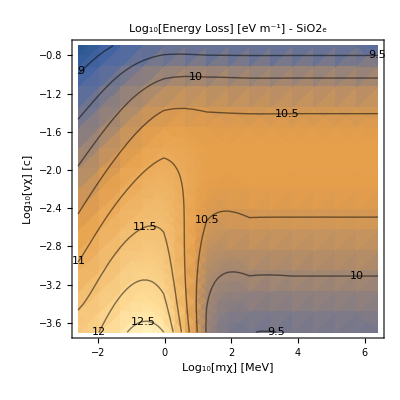

```mathematica
EnergyLoss`PlotEL[SiO2BGeDictSI,"SiO2_e"]
```

#### Run MgO

```mathematica
(*MgOλeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparams,True,"MgOλeDictSI"]*)
```

```mathematica
MgOTotalparamsBG=Table[Join[MgOTotalparams[[i]],{"ωBG"->(7.77 "JpereV")/("ℏ")/.SIConstRepl}],{i,Length[MgOTotalparams]}];
```

```mathematica
MgOBGeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparamsBG,True,"MgOBGeDictSI",-1]
```

1 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1987.19}. NIntegrate obtained 0.000337559 and 4.38616×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000337559 
Prefactor:	3.99192×10^13
dEdr:	1.34751×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1983.01}. NIntegrate obtained 0.000208341 and 1.08951×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000208341 
Prefactor:	5.73915×10^14
dEdr:	1.1957×10^11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000182741 and 4.01308×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000182741 
Prefactor:	4.00973×10^14
dEdr:	7.32741×10^10

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.0000668434 
Prefactor:	1.00279×10^16
dEdr:	6.703×10^11

dEdr total: 8.76619×10^11

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00337213 
Prefactor:	3.99192×10^11
dEdr:	1.34613×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00214005 
Prefactor:	5.73915×10^12
dEdr:	1.22821×10^10

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00183626 
Prefactor:	4.00973×10^12
dEdr:	7.36293×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000596438 
Prefactor:	1.00279×10^14
dEdr:	5.98103×10^10

dEdr total: 8.08015×10^10

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0339014 
Prefactor:	3.99192×10^9
dEdr:	1.35332×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0208949 
Prefactor:	5.73915×10^10
dEdr:	1.19919×10^9

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.018411 
Prefactor:	4.00973×10^10
dEdr:	7.38233×10^8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.006315 
Prefactor:	1.00279×10^12
dEdr:	6.33263×10^9

dEdr total: 8.40538×10^9

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.258079 
Prefactor:	3.99192×10^7
dEdr:	1.03023×10^7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.167196 
Prefactor:	5.73915×10^8
dEdr:	9.59562×10^7

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.150578 
Prefactor:	4.00973×10^8
dEdr:	6.03778×10^7

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.0592598 
Prefactor:	1.00279×10^10
dEdr:	5.94252×10^8

dEdr total: 7.60889×10^8

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00154969 
Prefactor:	3.99192×10^13
dEdr:	6.18623×10^10

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000950025 
Prefactor:	5.73915×10^14
dEdr:	5.45234×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000848748 
Prefactor:	4.00973×10^14
dEdr:	3.40325×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000302277 
Prefactor:	1.00279×10^16
dEdr:	3.03121×10^12

dEdr total: 3.97863×10^12

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0154786 
Prefactor:	3.99192×10^11
dEdr:	6.17895×10^9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00949283 
Prefactor:	5.73915×10^12
dEdr:	5.44808×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00848144 
Prefactor:	4.00973×10^12
dEdr:	3.40083×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00302172 
Prefactor:	1.00279×10^14
dEdr:	3.03015×10^11

dEdr total: 3.97683×10^11

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.143846 
Prefactor:	3.99192×10^9
dEdr:	5.74221×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0892545 
Prefactor:	5.73915×10^10
dEdr:	5.12246×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0800532 
Prefactor:	4.00973×10^10
dEdr:	3.20992×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0294892 
Prefactor:	1.00279×10^12
dEdr:	2.95715×10^10

dEdr total: 3.84781×10^10

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.541135 
Prefactor:	3.99192×10^7
dEdr:	2.16017×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.370804 
Prefactor:	5.73915×10^8
dEdr:	2.1281×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.340363 
Prefactor:	4.00973×10^8
dEdr:	1.36476×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.162661 
Prefactor:	1.00279×10^10
dEdr:	1.63115×10^9

dEdr total: 2.00204×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00167282 
Prefactor:	3.99192×10^13
dEdr:	6.67777×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00102198 
Prefactor:	5.73915×10^14
dEdr:	5.86528×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000910984 
Prefactor:	4.00973×10^14
dEdr:	3.6528×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000477238 
Prefactor:	1.00279×10^16
dEdr:	4.7857×10^12

dEdr total: 5.80429×10^12

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0195732 
Prefactor:	3.99192×10^11
dEdr:	7.81349×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0112008 
Prefactor:	5.73915×10^12
dEdr:	6.4283×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00987762 
Prefactor:	4.00973×10^12
dEdr:	3.96066×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00491014 
Prefactor:	1.00279×10^14
dEdr:	4.92384×10^11

dEdr total: 6.04087×10^11

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.386248 
Prefactor:	3.99192×10^9
dEdr:	1.54187×10^9

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.254789 
Prefactor:	5.73915×10^10
dEdr:	1.46227×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.231161 
Prefactor:	4.00973×10^10
dEdr:	9.26893×10^9

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0877213 
Prefactor:	1.00279×10^12
dEdr:	8.79662×10^10

dEdr total: 1.134×10^11

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.833349 
Prefactor:	3.99192×10^7
dEdr:	3.32667×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.589279 
Prefactor:	5.73915×10^8
dEdr:	3.38196×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.544685 
Prefactor:	4.00973×10^8
dEdr:	2.18404×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.291913 
Prefactor:	1.00279×10^10
dEdr:	2.92728×10^9

dEdr total: 3.51715×10^9

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	5.18221×10^-6 
Prefactor:	3.99192×10^13
dEdr:	2.0687×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.73418×10^-6 
Prefactor:	5.73915×10^14
dEdr:	1.56919×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.37642×10^-6 
Prefactor:	4.00973×10^14
dEdr:	9.52881×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.52113×10^-6 
Prefactor:	1.00279×10^16
dEdr:	1.52537×10^10

dEdr total: 1.79827×10^10

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00272641 
Prefactor:	3.99192×10^11
dEdr:	1.08836×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00088947 
Prefactor:	5.73915×10^12
dEdr:	5.1048×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000689596 
Prefactor:	4.00973×10^12
dEdr:	2.76509×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000241503 
Prefactor:	1.00279×10^14
dEdr:	2.42177×10^10

dEdr total: 3.3176×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.309188 
Prefactor:	3.99192×10^9
dEdr:	1.23425×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.195389 
Prefactor:	5.73915×10^10
dEdr:	1.12137×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.175057 
Prefactor:	4.00973×10^10
dEdr:	7.01931×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.051348 
Prefactor:	1.00279×10^12
dEdr:	5.14913×10^10

dEdr total: 7.09586×10^10

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.759537 
Prefactor:	3.99192×10^7
dEdr:	3.03201×10^7

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.53408 
Prefactor:	5.73915×10^8
dEdr:	3.06517×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.493046 
Prefactor:	4.00973×10^8
dEdr:	1.97698×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.258402 
Prefactor:	1.00279×10^10
dEdr:	2.59123×10^9

dEdr total: 3.12576×10^9

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.22165×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.28606×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.22057×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.00503×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	9.73437×10^-7 
Prefactor:	4.00973×10^14
dEdr:	3.90322×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.61604×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.62614×10^9

dEdr total: 4.84557×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00258961 
Prefactor:	3.99192×10^11
dEdr:	1.03375×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000795314 
Prefactor:	5.73915×10^12
dEdr:	4.56443×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000606709 
Prefactor:	4.00973×10^12
dEdr:	2.43274×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000196802 
Prefactor:	1.00279×10^14
dEdr:	1.97352×10^10

dEdr total: 2.77661×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.306379 
Prefactor:	3.99192×10^9
dEdr:	1.22304×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.19319 
Prefactor:	5.73915×10^10
dEdr:	1.10875×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.172968 
Prefactor:	4.00973×10^10
dEdr:	6.93556×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.0500891 
Prefactor:	1.00279×10^12
dEdr:	5.02289×10^10

dEdr total: 6.9475×10^10

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.756627 
Prefactor:	3.99192×10^7
dEdr:	3.0204×10^7

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.531988 
Prefactor:	5.73915×10^8
dEdr:	3.05316×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.491186 
Prefactor:	4.00973×10^8
dEdr:	1.96952×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.257201 
Prefactor:	1.00279×10^10
dEdr:	2.57919×10^9

dEdr total: 3.11166×10^9

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.32264×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.32637×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.26761×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.27504×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.01275×10^-6 
Prefactor:	4.00973×10^14
dEdr:	4.06084×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.7956×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.80619×10^9

dEdr total: 5.07242×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00258309 
Prefactor:	3.99192×10^11
dEdr:	1.03115×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000790921 
Prefactor:	5.73915×10^12
dEdr:	4.53922×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00060285 
Prefactor:	4.00973×10^12
dEdr:	2.41727×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000194794 
Prefactor:	1.00279×10^14
dEdr:	1.95338×10^10

dEdr total: 2.75214×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.306233 
Prefactor:	3.99192×10^9
dEdr:	1.22246×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.193077 
Prefactor:	5.73915×10^10
dEdr:	1.1081×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.172861 
Prefactor:	4.00973×10^10
dEdr:	6.93128×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.050025 
Prefactor:	1.00279×10^12
dEdr:	5.01646×10^10

dEdr total: 6.93993×10^10

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.756643 
Prefactor:	3.99192×10^7
dEdr:	3.02046×10^7

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.531981 
Prefactor:	5.73915×10^8
dEdr:	3.05312×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.49109 
Prefactor:	4.00973×10^8
dEdr:	1.96914×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.25714 
Prefactor:	1.00279×10^10
dEdr:	2.57857×10^9

dEdr total: 3.111×10^9

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.32846×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.3287×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.27043×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.29119×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.01512×10^-6 
Prefactor:	4.00973×10^14
dEdr:	4.07036×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.80739×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.81801×10^9

dEdr total: 5.08704×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00258268 
Prefactor:	3.99192×10^11
dEdr:	1.03099×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000790686 
Prefactor:	5.73915×10^12
dEdr:	4.53787×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000602645 
Prefactor:	4.00973×10^12
dEdr:	2.41645×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000194685 
Prefactor:	1.00279×10^14
dEdr:	1.95228×10^10

dEdr total: 2.75081×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.306226 
Prefactor:	3.99192×10^9
dEdr:	1.22243×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.193071 
Prefactor:	5.73915×10^10
dEdr:	1.10807×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.172856 
Prefactor:	4.00973×10^10
dEdr:	6.93106×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.0500216 
Prefactor:	1.00279×10^12
dEdr:	5.01612×10^10

dEdr total: 6.93953×10^10

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.756635 
Prefactor:	3.99192×10^7
dEdr:	3.02043×10^7

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.531975 
Prefactor:	5.73915×10^8
dEdr:	3.05309×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.491085 
Prefactor:	4.00973×10^8
dEdr:	1.96912×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.257136 
Prefactor:	1.00279×10^10
dEdr:	2.57854×10^9

dEdr total: 3.11097×10^9

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.32876×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.32882×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.27058×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.29203×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.01524×10^-6 
Prefactor:	4.00973×10^14
dEdr:	4.07086×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.808×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.81863×10^9

dEdr total: 5.0878×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00258268 
Prefactor:	3.99192×10^11
dEdr:	1.03099×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000790679 
Prefactor:	5.73915×10^12
dEdr:	4.53783×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000602635 
Prefactor:	4.00973×10^12
dEdr:	2.4164×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000194682 
Prefactor:	1.00279×10^14
dEdr:	1.95226×10^10

dEdr total: 2.75078×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.306225 
Prefactor:	3.99192×10^9
dEdr:	1.22243×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.193071 
Prefactor:	5.73915×10^10
dEdr:	1.10806×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.172856 
Prefactor:	4.00973×10^10
dEdr:	6.93104×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.0500214 
Prefactor:	1.00279×10^12
dEdr:	5.01611×10^10

dEdr total: 6.93952×10^10

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.756636 
Prefactor:	3.99192×10^7
dEdr:	3.02043×10^7

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.531975 
Prefactor:	5.73915×10^8
dEdr:	3.05309×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.491085 
Prefactor:	4.00973×10^8
dEdr:	1.96912×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.257136 
Prefactor:	1.00279×10^10
dEdr:	2.57854×10^9

dEdr total: 3.11097×10^9

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{8.76619×10^11,8.08015×10^10,8.40538×10^9,7.60889×10^8},{3.97863×10^12,3.97683×10^11,3.84781×10^10,2.00204×10^9},{5.80429×10^12,6.04087×10^11,1.134×10^11,3.51715×10^9},{1.79827×10^10,3.3176×10^10,7.09586×10^10,3.12576×10^9},{4.84557×10^9,2.77661×10^10,6.9475×10^10,3.11166×10^9},{5.07242×10^9,2.75214×10^10,6.93993×10^10,3.111×10^9},{5.08704×10^9,2.75081×10^10,6.93953×10^10,3.11097×10^9},{5.0878×10^9,2.75078×10^10,6.93952×10^10,3.11097×10^9}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→412.839,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0,ωBG→1.17986×10^16},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→736.197,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0,ωBG→1.17986×10^16},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→841.135,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0,ωBG→1.17986×10^16},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.61838×10^30,qF→3.63218×10^10,vF→4.20631×10^6,μ→8.05919×10^-18,ωp→7.18146×10^16,α→1/137,χ→0.407075,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2012.33,nI→2.02298×10^29,Z→8,M→9.27329×10^-26,EF→8.05919×10^-18,ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0,ωBG→1.17986×10^16}},fname→MgOBGeDictSI,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{783.551,974.098,1096.77,2293.51},{60.4057,75.6296,364.037,1303.5},{58.4316,83.026,618.212,555.039},{47.0952,158.017,540.926,602.304},{90.4791,108.085,717.256,1152.14},{165.422,244.451,1296.4,1147.49},{148.439,106.968,399.119,381.323},{56.1558,94.8183,409.796,399.576}},totalTime→16532.5|>

#### Plot MgO

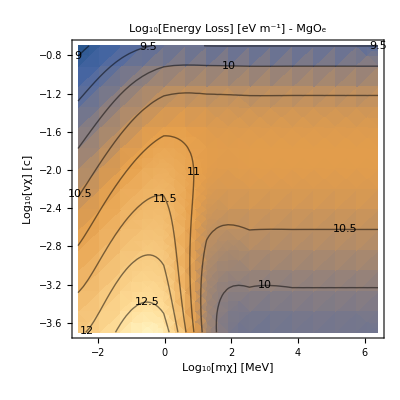

```mathematica
EnergyLoss`PlotEL[MgOBGeDictSI,"MgO_e"]
```

### Compare to total EL

#### Load EL Dicts

```mathematica
SiO2ELTotalDict = ReadIt[NotebookDirectory[]<>"../../ELandKappamin/compute energy loss/SiO2ELOutputDictSIwiderm"];
MgOELTotalDict = ReadIt[NotebookDirectory[]<>"../../ELandKappamin/compute energy loss/MgOELOutputDictSIwiderm"];
```

#### Make a dict with ratios

```mathematica
SiO2TotToBBG = SiO2ELTotalDict;
TempRatFuncSiO2[mχ_,vχ_]:=SiO2ELTotalDict[["f"]][mχ,vχ]-SiO2BGeDictSI[["f"]][mχ,vχ]
SiO2TotToBBG[["f"]] = TempRatFuncSiO2;
```

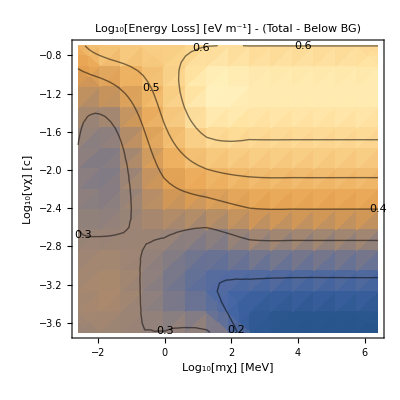

```mathematica
PlotEL[SiO2TotToBBG,"(Total -  Below BG)"]
```

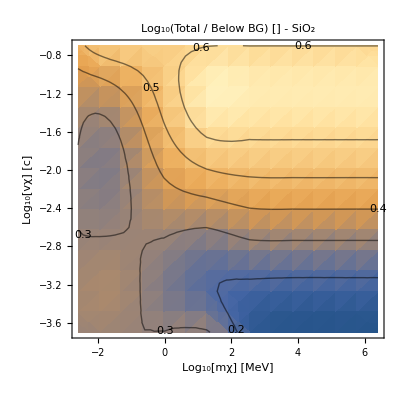

```mathematica
PlotEL[SiO2TotToBBG,"(Total -  Below BG)",True,"Log_10(Total / Below BG) [] - SiO_2"]
```

```mathematica
(10^0.1)^6
```

3.98107

```mathematica
MgOTotToBBG = MgOELTotalDict;
TempRatFunc[mχ_,vχ_]:=MgOELTotalDict[["f"]][mχ,vχ]-MgOBGeDictSI[["f"]][mχ,vχ]
MgOTotToBBG[["f"]] = TempRatFunc;
```

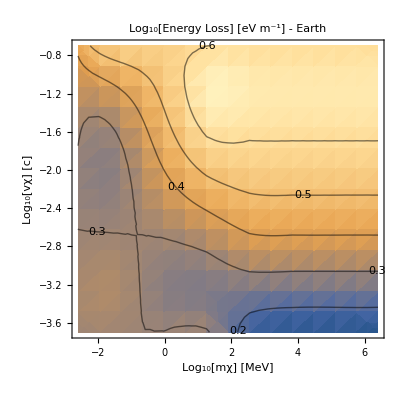

```mathematica
PlotEL[MgOTotToBBG]
```

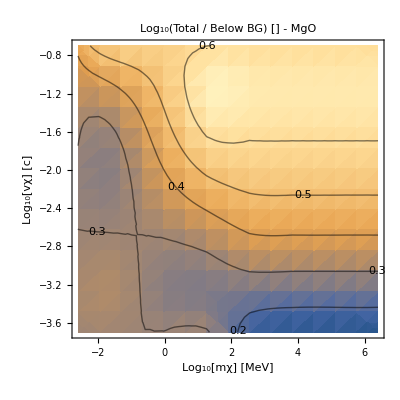

```mathematica
PlotEL[MgOTotToBBG,"(Total -  Below BG)",True,"Log_10(Total / Below BG) [] - MgO"]
```

## Post ω fix

### Compute contribution from below the band gap

#### Run SiO2

```mathematica
SiO2TotalparamsBG=Table[Join[SiO2Totalparams[[i]],{"ωBG"->(8.96 "JpereV")/("ℏ")/.SIConstRepl}],{i,Length[SiO2Totalparams]}];
```

```mathematica
SiO2BGeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,SiO2TotalparamsBG,True,"SiO2BGeDictSI",-1]
```

1 of 32

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000616587}. NIntegrate obtained -8.73754×10^-19 and 2.04963×10^-18 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	-8.73754×10^-19 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	-0.00182543

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000416375}. NIntegrate obtained -1.38841×10^-21 and 2.1498×10^-20 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	-1.38841×10^-21 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	-3.85198×10^-6

dEdr total: -0.00182928

2 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000099157}. NIntegrate obtained 1.61818×10^-12 and 1.50777×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	1.61818×10^-12 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	33.8067

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	1.01307×10^-13 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	2.81065

dEdr total: 36.6174

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	1.71706×10^-7 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	35872.5

For mχ = 4.45×10^-33 , vχ = 6000000
L:	1.18112×10^-8 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	3276.87

dEdr total: 39149.3

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.00356502 
Prefactor:	2.08918×10^9
 (RowBox[{)^th E moment:	7.44798×10^6

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.000218621 
Prefactor:	2.77438×10^9
 (RowBox[{)^th E moment:	606538.

dEdr total: 8.05451×10^6

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	5.99674×10^-14 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	125.283

For mχ = 8.5916×10^-32 , vχ = 60000
L:	3.96201×10^-15 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	10.9921

dEdr total: 136.275

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	1.44154×10^-9 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	30116.4

For mχ = 8.5916×10^-32 , vχ = 600000
L:	9.91639×10^-11 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	2751.18

dEdr total: 32867.6

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00126958 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	2.65239×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0000794903 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	2.20536×10^7

dEdr total: 2.87292×10^8

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.00519924 
Prefactor:	2.08918×10^9
 (RowBox[{)^th E moment:	1.08622×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.00033282 
Prefactor:	2.77438×10^9
 (RowBox[{)^th E moment:	923368.

dEdr total: 1.17855×10^7

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	2.71×10^-11 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	56616.9

For mχ = 1.65878×10^-30 , vχ = 60000
L:	1.8633×10^-12 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	5169.48

dEdr total: 61786.4

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	8.64356×10^-6 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	1.8058×10^8

For mχ = 1.65878×10^-30 , vχ = 600000
L:	5.77319×10^-7 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	1.6017×10^7

dEdr total: 1.96597×10^8

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.00273049 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	5.70448×10^8

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.000182353 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	5.05917×10^7

dEdr total: 6.2104×10^8

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.00520134 
Prefactor:	2.08918×10^9
 (RowBox[{)^th E moment:	1.08666×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.000331261 
Prefactor:	2.77438×10^9
 (RowBox[{)^th E moment:	919044.

dEdr total: 1.17856×10^7

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	5.13253×10^-8 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	1.07228×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	3.55602×10^-9 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	9.86574×10^6

dEdr total: 1.17094×10^8

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000439197 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	9.17563×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.0000384618 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	1.06707×10^9

dEdr total: 1.02427×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.00273943 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	5.72316×10^8

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.000182892 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	5.07412×10^7

dEdr total: 6.23057×10^8

16 of 32

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.2.08918×10^9
 (RowBox[{)^th E moment:	0.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.2.77438×10^9
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	7.93995×10^-7 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	1.6588×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.2611×10^-7 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	3.49876×10^8

dEdr total: 2.00868×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000471736 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	9.85541×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0000407421 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	1.13034×10^9

dEdr total: 1.09858×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.00274102 
Prefactor:	2.08918×10^11
 (RowBox[{)^th E moment:	5.7265×10^8

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.000182993 
Prefactor:	2.77438×10^11
 (RowBox[{)^th E moment:	5.07691×10^7

dEdr total: 6.23419×10^8

20 of 32

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.2.08918×10^9
 (RowBox[{)^th E moment:	0.

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.2.77438×10^9
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	8.99095×10^-7 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	1.87837×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.53624×10^-7 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	4.26212×10^8

dEdr total: 2.30458×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000473413 
Prefactor:	2.08918×10^13
 (RowBox[{)^th E moment:	9.89045×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.0000408619 
Prefactor:	2.77438×10^13
 (RowBox[{)^th E moment:	1.13366×10^9

dEdr total: 1.10241×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.2.08918×10^11
 (RowBox[{)^th E moment:	0.

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.2.77438×10^11
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.2.08918×10^9
 (RowBox[{)^th E moment:	0.

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.2.77438×10^9
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	9.03511×10^-7 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	1.8876×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.55158×10^-7 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	4.30467×10^8

dEdr total: 2.31806×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.2.08918×10^13
 (RowBox[{)^th E moment:	0.

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.2.77438×10^13
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.2.08918×10^11
 (RowBox[{)^th E moment:	0.

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.2.77438×10^11
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.2.08918×10^9
 (RowBox[{)^th E moment:	0.

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.2.77438×10^9
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	9.05661×10^-7 
Prefactor:	2.08918×10^15
 (RowBox[{)^th E moment:	1.89209×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.55235×10^-7 
Prefactor:	2.77438×10^15
 (RowBox[{)^th E moment:	4.30681×10^8

dEdr total: 2.32277×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.2.08918×10^13
 (RowBox[{)^th E moment:	0.

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.2.77438×10^13
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.2.08918×10^11
 (RowBox[{)^th E moment:	0.

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.2.77438×10^11
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.2.08918×10^9
 (RowBox[{)^th E moment:	0.

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.2.77438×10^9
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{-0.00182928,36.6174,39149.3,8.05451×10^6},{136.275,32867.6,2.87292×10^8,1.17855×10^7},{61786.4,1.96597×10^8,6.2104×10^8,1.17856×10^7},{1.17094×10^8,1.02427×10^10,6.23057×10^8,0.},{2.00868×10^9,1.09858×10^10,6.23419×10^8,0.},{2.30458×10^9,1.10241×10^10,0.,0.},{2.31806×10^9,0.,0.,0.},{2.32277×10^9,0.,0.,0.}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωBG→1.36056×10^16},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2326.72,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0,ωBG→1.36056×10^16}},fname→SiO2BGeDictSI,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{1307.,318.013,182.23,104.553},{338.232,219.598,59.8145,245.89},{353.285,22.7031,221.193,149.51},{21.3115,35.1191,87.4691,1.61432},{21.607,98.6715,63.8623,0.989176},{48.9261,39.5089,0.709366,0.700126},{74.9427,1.14501,1.1156,1.10325},{48.6529,1.37936,1.19669,1.2524}},totalTime→4073.3|>

#### Plot SiO2

```mathematica
EnergyLoss`PlotEL[SiO2BGeDictSI,"SiO2_e"]
```

-Graphics-

#### Run MgO

```mathematica
(*MgOλeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparams,True,"MgOλeDictSI"]*)
```

```mathematica
MgOTotalparamsBG=Table[Join[MgOTotalparams[[i]],{"ωBG"->(7.77 "JpereV")/("ℏ")/.SIConstRepl}],{i,Length[MgOTotalparams]}];
```

```mathematica
MgOBGeDictSI= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparamsBG,True,"MgOBGeDictSI",-1]
```

1 of 32

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000486715}. NIntegrate obtained 2.11303×10^-16 and 2.56787×10^-17 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	2.11303×10^-16 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	0.00843506

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000429724}. NIntegrate obtained 3.2963×10^-17 and 4.83587×10^-18 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	3.2963×10^-17 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	0.018918

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0000355717}. NIntegrate obtained 2.00662×10^-17 and 2.16288×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	2.00662×10^-17 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	0.00804602

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	2.70409×10^-21 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	0.0000271164

dEdr total: 0.0354262

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	3.45117×10^-12 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	1.37768

For mχ = 4.45×10^-33 , vχ = 600000
L:	5.43559×10^-13 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	3.11957

For mχ = 4.45×10^-33 , vχ = 600000
L:	3.51632×10^-13 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	1.40995

For mχ = 4.45×10^-33 , vχ = 600000
L:	2.46016×10^-13 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	24.6702

dEdr total: 30.5774

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	3.53381×10^-7 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	1410.67

For mχ = 4.45×10^-33 , vχ = 6000000
L:	5.56519×10^-8 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	3193.95

For mχ = 4.45×10^-33 , vχ = 6000000
L:	3.60351×10^-8 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	1444.91

For mχ = 4.45×10^-33 , vχ = 6000000
L:	3.63853×10^-8 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	36486.9

dEdr total: 42536.4

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.00642825 
Prefactor:	3.99192×10^7
 (RowBox[{)^th E moment:	256611.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.000835687 
Prefactor:	5.73915×10^8
 (RowBox[{)^th E moment:	479613.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.000531681 
Prefactor:	4.00973×10^8
 (RowBox[{)^th E moment:	213190.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.000443775 
Prefactor:	1.00279×10^10
 (RowBox[{)^th E moment:	4.45014×10^6

dEdr total: 5.39956×10^6

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	1.23861×10^-13 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	4.94444

For mχ = 8.5916×10^-32 , vχ = 60000
L:	1.94887×10^-14 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	11.1849

For mχ = 8.5916×10^-32 , vχ = 60000
L:	1.26164×10^-14 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	5.05885

For mχ = 8.5916×10^-32 , vχ = 60000
L:	1.14537×10^-14 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	114.856

dEdr total: 136.045

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	2.98474×10^-9 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	1191.49

For mχ = 8.5916×10^-32 , vχ = 600000
L:	4.71293×10^-10 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	2704.83

For mχ = 8.5916×10^-32 , vχ = 600000
L:	3.05404×10^-10 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	1224.59

For mχ = 8.5916×10^-32 , vχ = 600000
L:	3.05471×10^-10 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	30632.4

dEdr total: 35753.3

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00291522 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	1.16373×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.000442477 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	2.53944×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.000290237 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	1.16377×10^7

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.000184646 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	1.85161×10^8

dEdr total: 2.33831×10^8

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.0104738 
Prefactor:	3.99192×10^7
 (RowBox[{)^th E moment:	418105.

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.00164425 
Prefactor:	5.73915×10^8
 (RowBox[{)^th E moment:	943661.

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.00109192 
Prefactor:	4.00973×10^8
 (RowBox[{)^th E moment:	437829.

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.000628856 
Prefactor:	1.00279×10^10
 (RowBox[{)^th E moment:	6.30611×10^6

dEdr total: 8.10571×10^6

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	5.73834×10^-11 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	2290.7

For mχ = 1.65878×10^-30 , vχ = 60000
L:	9.11908×10^-12 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	5233.58

For mχ = 1.65878×10^-30 , vχ = 60000
L:	5.92185×10^-12 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	2374.5

For mχ = 1.65878×10^-30 , vχ = 60000
L:	5.7371×10^-12 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	57531.1

dEdr total: 67429.9

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0000320185 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	1.27815×10^7

For mχ = 1.65878×10^-30 , vχ = 600000
L:	5.84627×10^-6 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	3.35526×10^7

For mχ = 1.65878×10^-30 , vχ = 600000
L:	3.94049×10^-6 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	1.58003×10^7

For mχ = 1.65878×10^-30 , vχ = 600000
L:	1.64857×10^-6 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	1.65317×10^8

dEdr total: 2.27452×10^8

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0062378 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	2.49008×10^7

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.00111795 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	6.4161×10^7

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.000760467 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	3.04927×10^7

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.000336252 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	3.37191×10^8

dEdr total: 4.56745×10^8

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.0104762 
Prefactor:	3.99192×10^7
 (RowBox[{)^th E moment:	418203.

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.00164412 
Prefactor:	5.73915×10^8
 (RowBox[{)^th E moment:	943588.

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.0010915 
Prefactor:	4.00973×10^8
 (RowBox[{)^th E moment:	437664.

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.000626185 
Prefactor:	1.00279×10^10
 (RowBox[{)^th E moment:	6.27932×10^6

dEdr total: 8.07878×10^6

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.14064×10^-7 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	8.54528×10^6

For mχ = 3.2026×10^-29 , vχ = 60000
L:	4.31587×10^-8 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	2.47695×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.97574×10^-8 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	1.19319×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	9.12407×10^-9 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	9.14954×10^7

dEdr total: 1.36742×10^8

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.0013466 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	5.37552×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000340405 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	1.95364×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000245425 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	9.84087×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.0000646326 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	6.4813×10^9

dEdr total: 9.95657×10^9

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.00624641 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	2.49352×10^7

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.0011194 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	6.42441×10^7

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.000761393 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	3.05298×10^7

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.000337145 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	3.38087×10^8

dEdr total: 4.57796×10^8

16 of 32

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.3.99192×10^7
 (RowBox[{)^th E moment:	0.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.5.73915×10^8
 (RowBox[{)^th E moment:	0.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.4.00973×10^8
 (RowBox[{)^th E moment:	0.

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.1.00279×10^10
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	2.07402×10^-6 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	8.27935×10^7

For mχ = 6.18325×10^-28 , vχ = 60000
L:	7.62975×10^-7 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	4.37883×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	6.03931×10^-7 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	2.4216×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	2.15117×10^-7 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	2.15717×10^9

dEdr total: 2.92001×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00143835 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	5.74178×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000358493 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	2.05745×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000257885 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	1.03405×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0000680189 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	6.82087×10^9

dEdr total: 1.04865×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.00625465 
Prefactor:	3.99192×10^9
 (RowBox[{)^th E moment:	2.49681×10^7

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.0011199 
Prefactor:	5.73915×10^10
 (RowBox[{)^th E moment:	6.4273×10^7

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.000761697 
Prefactor:	4.00973×10^10
 (RowBox[{)^th E moment:	3.0542×10^7

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.000337248 
Prefactor:	1.00279×10^12
 (RowBox[{)^th E moment:	3.3819×10^8

dEdr total: 4.57973×10^8

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.3.99192×10^7
 (RowBox[{)^th E moment:	0.

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.5.73915×10^8
 (RowBox[{)^th E moment:	0.

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.4.00973×10^8
 (RowBox[{)^th E moment:	0.

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.1.00279×10^10
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.28159×10^-6 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	9.10793×10^7

For mχ = 1.1938×10^-26 , vχ = 60000
L:	8.63439×10^-7 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	4.95541×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	6.88018×10^-7 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	2.75877×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.56582×10^-7 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	2.57298×10^9

dEdr total: 3.43548×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00144277 
Prefactor:	3.99192×10^11
 (RowBox[{)^th E moment:	5.75942×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000359472 
Prefactor:	5.73915×10^12
 (RowBox[{)^th E moment:	2.06306×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000258543 
Prefactor:	4.00973×10^12
 (RowBox[{)^th E moment:	1.03669×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.0000682152 
Prefactor:	1.00279×10^14
 (RowBox[{)^th E moment:	6.84056×10^9

dEdr total: 1.05163×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.3.99192×10^9
 (RowBox[{)^th E moment:	0.

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.5.73915×10^10
 (RowBox[{)^th E moment:	0.

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.4.00973×10^10
 (RowBox[{)^th E moment:	0.

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.1.00279×10^12
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.3.99192×10^7
 (RowBox[{)^th E moment:	0.

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.5.73915×10^8
 (RowBox[{)^th E moment:	0.

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.4.00973×10^8
 (RowBox[{)^th E moment:	0.

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.1.00279×10^10
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.28206×10^-6 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	9.10981×10^7

For mχ = 2.30487×10^-25 , vχ = 60000
L:	8.82404×10^-7 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	5.06425×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	6.79874×10^-7 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	2.72611×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.58906×10^-7 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	2.59629×10^9

dEdr total: 3.46642×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.3.99192×10^11
 (RowBox[{)^th E moment:	0.

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.5.73915×10^12
 (RowBox[{)^th E moment:	0.

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.4.00973×10^12
 (RowBox[{)^th E moment:	0.

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.1.00279×10^14
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.3.99192×10^9
 (RowBox[{)^th E moment:	0.

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.5.73915×10^10
 (RowBox[{)^th E moment:	0.

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.4.00973×10^10
 (RowBox[{)^th E moment:	0.

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.1.00279×10^12
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.3.99192×10^7
 (RowBox[{)^th E moment:	0.

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.5.73915×10^8
 (RowBox[{)^th E moment:	0.

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.4.00973×10^8
 (RowBox[{)^th E moment:	0.

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.1.00279×10^10
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.28959×10^-6 
Prefactor:	3.99192×10^13
 (RowBox[{)^th E moment:	9.13986×10^7

For mχ = 4.45×10^-24 , vχ = 60000
L:	8.69055×10^-7 
Prefactor:	5.73915×10^14
 (RowBox[{)^th E moment:	4.98764×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	6.93232×10^-7 
Prefactor:	4.00973×10^14
 (RowBox[{)^th E moment:	2.77968×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.58964×10^-7 
Prefactor:	1.00279×10^16
 (RowBox[{)^th E moment:	2.59687×10^9

dEdr total: 3.465×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.3.99192×10^11
 (RowBox[{)^th E moment:	0.

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.5.73915×10^12
 (RowBox[{)^th E moment:	0.

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.4.00973×10^12
 (RowBox[{)^th E moment:	0.

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.1.00279×10^14
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.3.99192×10^9
 (RowBox[{)^th E moment:	0.

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.5.73915×10^10
 (RowBox[{)^th E moment:	0.

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.4.00973×10^10
 (RowBox[{)^th E moment:	0.

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.1.00279×10^12
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.3.99192×10^7
 (RowBox[{)^th E moment:	0.

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.5.73915×10^8
 (RowBox[{)^th E moment:	0.

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.4.00973×10^8
 (RowBox[{)^th E moment:	0.

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.1.00279×10^10
 (RowBox[{)^th E moment:	0.

dEdr total: 0.

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{0.0354262,30.5774,42536.4,5.39956×10^6},{136.045,35753.3,2.33831×10^8,8.10571×10^6},{67429.9,2.27452×10^8,4.56745×10^8,8.07878×10^6},{1.36742×10^8,9.95657×10^9,4.57796×10^8,0.},{2.92001×10^9,1.04865×10^10,4.57973×10^8,0.},{3.43548×10^9,1.05163×10^10,0.,0.},{3.46642×10^9,0.,0.,0.},{3.465×10^9,0.,0.,0.}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→412.839,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0,ωBG→1.17986×10^16},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→736.197,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0,ωBG→1.17986×10^16},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→841.135,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0,ωBG→1.17986×10^16},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.61838×10^30,qF→3.63218×10^10,vF→4.20631×10^6,μ→8.05919×10^-18,ωp→7.18146×10^16,α→1/137,χ→0.407075,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2012.33,nI→2.02298×10^29,Z→8,M→9.27329×10^-26,EF→8.05919×10^-18,ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0,ωBG→1.17986×10^16}},fname→MgOBGeDictSI,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{3740.49,2533.23,702.912,982.863},{1991.81,957.375,352.274,561.591},{496.876,36.3909,474.634,730.756},{85.743,297.169,377.865,5.32871},{132.048,350.64,344.482,5.22163},{323.157,302.115,5.41151,5.42806},{513.423,5.49258,5.38416,5.78153},{205.636,5.4334,5.39837,5.50069}},totalTime→16547.9|>

#### Plot MgO

```mathematica
EnergyLoss`PlotEL[MgOBGeDictSI,"MgO_e"]
```

-Graphics-

### Compare to total EL

#### Load EL Dicts

```mathematica
SiO2ELTotalDict = ReadIt[NotebookDirectory[]<>"../../ELandKappamin/compute energy loss/SiO2ELOutputDictSIEnhanced"];
MgOELTotalDict = ReadIt[NotebookDirectory[]<>"../../ELandKappamin/compute energy loss/MgOELOutputDictSIEnhanced"];
```

#### Make a dict with ratios

```mathematica
SiO2TotToBBG = SiO2ELTotalDict;
TempRatFuncSiO2[mχ_,vχ_]:=SiO2ELTotalDict[["f"]][mχ,vχ]-SiO2BGeDictSI[["f"]][mχ,vχ]
SiO2TotToBBG[["f"]] = TempRatFuncSiO2;
```

```mathematica
PlotEL[SiO2TotToBBG,"(Total -  Below BG)"]
```

-Graphics-

```mathematica
PlotEL[SiO2TotToBBG,"(Total -  Below BG)",True,"Log_10(Total / Below BG) [] - SiO_2"]
```

-Graphics-

```mathematica
MgOTotToBBG = MgOELTotalDict;
TempRatFunc[mχ_,vχ_]:=MgOELTotalDict[["f"]][mχ,vχ]-MgOBGeDictSI[["f"]][mχ,vχ]
MgOTotToBBG[["f"]] = TempRatFunc;
```

```mathematica
PlotEL[MgOTotToBBG,"(Total -  Below BG)",True,"Log_10(Total / Below BG) [] - MgO"]
```

-Graphics-